```mathematica
(*In this note, the penetration length λ does not change its absolute value but only changes with its phase θ.*)
```

```mathematica
ρ=0.01;

M[t1_,t2_,t3_,k1_,E_,θ_]:={{E,-(t1+2ⅈ t3 ⅇ^(-ⅈ k1))-ⅈ t3 ρ(Cos[θ]+Sin[θ]ⅈ),-t2 ⅇ^(-ⅈ k1),-(t1-2ⅈ t3 ⅇ^(-ⅈ k1))-ⅈ t3/(ρ(Cos[θ]+Sin[θ]ⅈ)) },{-(t1-2ⅈ t3 ⅇ^(ⅈ k1))+ⅈ t3/(ρ(Cos[θ]+Sin[θ]ⅈ)), E, -(t1+2ⅈ t3 ⅇ^(-ⅈ k1))-ⅈ t3/(ρ(Cos[θ]+Sin[θ]ⅈ)) ,-t2 /(ρ(Cos[θ]+Sin[θ]ⅈ)) },{-t2 ⅇ^(ⅈ k1),-(t1-2ⅈ t3 ⅇ^(ⅈ k1))+ⅈ t3 ρ(Cos[θ]+Sin[θ]ⅈ),E,-(t1+2ⅈ t3 ⅇ^(ⅈ k1))-ⅈ t3/(ρ(Cos[θ]+Sin[θ]ⅈ)) },{-(t1+2ⅈ t3 ⅇ^(ⅈ k1))-ⅈ t3 (ρ(Cos[θ]+Sin[θ]ⅈ)),-t2 (ρ(Cos[θ]+Sin[θ]ⅈ)),-(t1-2ⅈ t3 ⅇ^(-ⅈ k1))+ⅈ t3 (ρ(Cos[θ]+Sin[θ]ⅈ)),E}};
```

```mathematica
With[{t1=0.8,t2=1.0,t3=0.01,E=0.4},M1=M[t1,t2,t3,k1,E,α]];
```

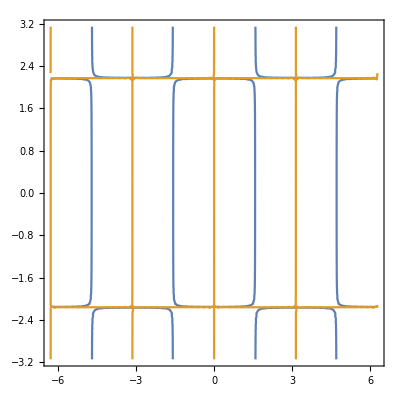

```mathematica
ContourPlot[{Re[Det[M1]]==0,Im[Det[M1]]==0},{α,-2π,2π},{k1,-π,π}]
```